## Analysis of the Completeness and Efficiency of Quantum and Classical Gates

## Abstract: This project begins by exploring classical logic gate structures, focusing on two-input one-output (2→1) and two-input two-output (2→2) gates to identify all functionally distinct pairs of classical operations. This analysis lays the foundation for understanding complexity and universality in small gate systems. We then extend this framework into the quantum regime, classifying all two-qubit quantum gates using the Cartan (KAK) decomposition. Each quantum gate is mapped to a canonical triple within the Weyl chamber, a reduced geometric region that captures non-local behavior up to local unitary equivalence. The chamber is discretized at fixed resolution, and representative gates are generated for each point. Using Mikhlin invariants, we determine which gates are locally equivalent to universal entangling gates such as CNOT and the one with the highest efficiency. Visualizations include 3D plots of the Weyl chamber and 2D projections of quantum state transformations under these gates, offering a geometric and algebraic perspective on gate classification and universality across classical and quantum systems. Introduction

Classical 2→1 gates take two input bits and produce a single output bit, representing Boolean functions over four possible input 	combinations. There are 2^4 = 16 such gates, including familiar operations like AND, OR, XOR, and NAND. Among these, gates like NAND are universal, meaning they can be composed to construct any Boolean function. This classical notion of universality serves  as a foundation for understanding universality in quantum computation, where certain two-qubit gates, when paired with local operations, can generate any unitary transformation.

Proof of functional Completeness: Constructing All 2→1 Gates Using NAND

This code highlights the universality of NAND gates by constructing and visualizing all other 16 2x1 gates solely from NAND operations.

```mathematica
parseNandArgs[expr_String]:=Module[{inside,level=0,commaPos=0},inside=StringTake[expr,{6,-2}];
Do[Switch[StringTake[inside,{i}],"(",level++,")",level--,",",If[level==0,commaPos=i;Break[]]],{i,StringLength[inside]}];
If[commaPos==0,Return[{}]];
{StringTrim[StringTake[inside,commaPos-1]],StringTrim[StringTake[inside,{commaPos+1,StringLength[inside]}]]}];
```

Extracts the two arguments from a NAND(...) string while correctly handling nested parentheses.

```mathematica
inputPairs=Tuples[{0,1},2];
allFuncs=Tuples[{0,1},4];
NAND[a_,b_]:=1-a*b
```

Generates all possible 2-bit input pairs, defines all 2-input Boolean functions, and defines the NAND operation.

```mathematica
evalFunc[func_,a_,b_]:=Module[{idx},idx=Position[inputPairs,{a,b}][[1,1]];
func[[idx]]]

applyNandOnFuncs[f1_,f2_]:=Table[NAND[evalFunc[f1,a,b],evalFunc[f2,a,b]],{a,0,1},{b,0,1}]//Flatten

toFuncForm[list_]:=Partition[list,4][[1]]
```

Evaluates Boolean functions on input pairs, applies the NAND gate to two functions over all inputs, and formats the result as a 4-entry truth table.

```mathematica
expr0="NAND(NAND(NAND(a,a),a),NAND(NAND(a,a),a))";
expr1="NAND(NAND(a,a),a)";
exprA="a";
exprB="b";

baseExprs=Association[{0,0,0,0}->expr0,{1,1,1,1}->expr1,{0,1,0,1}->exprA,{0,0,1,1}->exprB];

generated=Keys[baseExprs];
expressions=baseExprs;
queue=generated;
```

Defines NAND-based expressions for constant and input functions, initializes the expression map, and sets up the queue for generating all Boolean functions.

```mathematica
While[Length[generated]<Length[allFuncs],f1=First[queue];
queue=Rest[queue];
Do[f2=g;
newFunc=toFuncForm[applyNandOnFuncs[f1,f2]];
If[!MemberQ[generated,newFunc],AppendTo[generated,newFunc];
expressions[newFunc]="NAND("<>expressions[f1]<>", "<>expressions[f2]<>")";
AppendTo[queue,newFunc];];
newFuncRev=toFuncForm[applyNandOnFuncs[f2,f1]];
If[!MemberQ[generated,newFuncRev],AppendTo[generated,newFuncRev];
expressions[newFuncRev]="NAND("<>expressions[f2]<>", "<>expressions[f1]<>")";
AppendTo[queue,newFuncRev];];,{g,generated}]];
```

Builds all 2-input Boolean functions by iteratively combining previously generated ones using the NAND operation in all input orders.

```mathematica
drawCircuit[exprStr_]:=Module[{id=1,wires={},nodes={},build},build[expr_]:=Which[StringMatchQ[expr,"a"|"b"],id++;nodes=Append[nodes,ToString[id]->expr];ToString[id],StringStartsQ[expr,"NAND("],Module[{args,left,right,thisID},args=parseNandArgs[expr];
If[Length[args]!=2,id++;nodes=Append[nodes,ToString[id]->"?"];
Return[ToString[id]]];
left=build[args[[1]]];
right=build[args[[2]]];
thisID=ToString[++id];
nodes=Append[nodes,thisID->"NAND"];
wires=Join[wires,{left->thisID,right->thisID}];
thisID],True,id++;nodes=Append[nodes,ToString[id]->"?"];ToString[id]];
id=0;wires={};nodes={};
build[exprStr];
Graph[wires,VertexLabels->Table[nodes[[i,1]]->Placed[If[nodes[[i,2]]==="NAND",Style[nodes[[i,2]],FontSize->12],Style[nodes[[i,2]],FontSize->16,Bold]],Above],{i,Length[nodes]}],VertexStyle->LightBlue,VertexSize->Medium,GraphLayout->"LayeredDigraphEmbedding"]];
```

Generates a circuit diagram as a graph from a NAND expression string

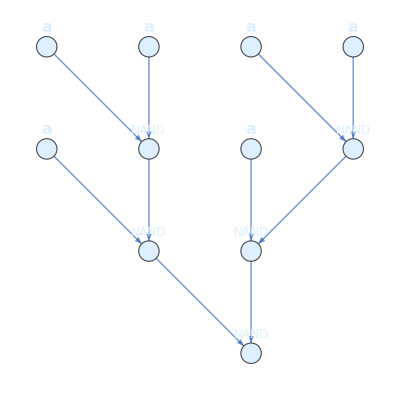
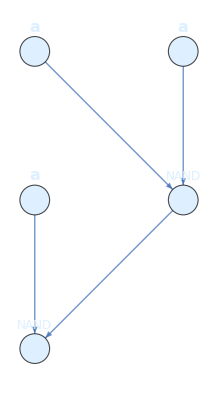
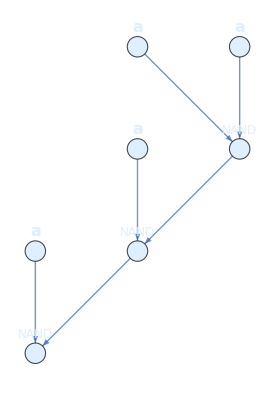
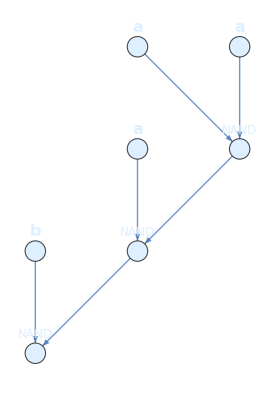
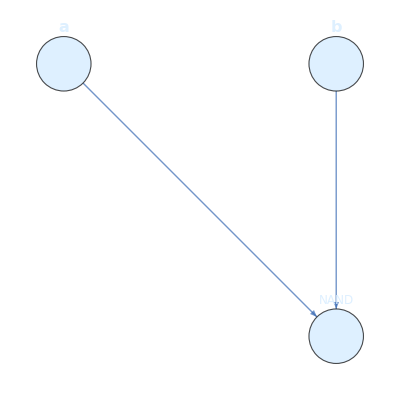
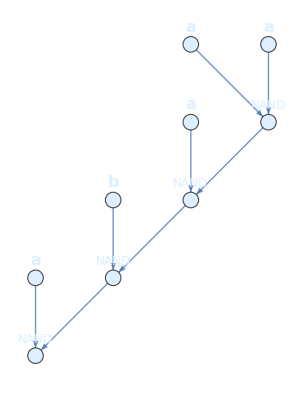
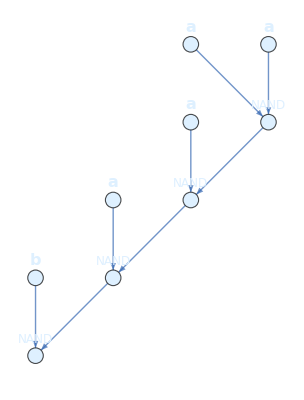
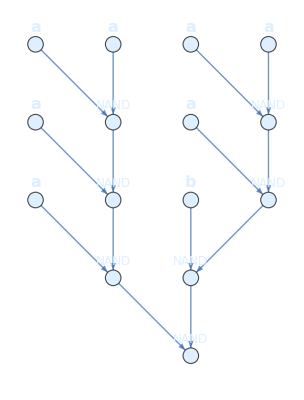
Truth Table | NAND Expression | Circuit Diagram
0
0
0
0 | NAND(NAND(NAND(a,a),a),NAND(NAND(a,a),a)) | -Graphics-
---------------- | ---------------- | ----------------
1
1
1
1 | NAND(NAND(a,a),a) | -Graphics-
---------------- | ---------------- | ----------------
0
1
0
1 | a | -Graphics-
---------------- | ---------------- | ----------------
0
0
1
1 | b | -Graphics-
---------------- | ---------------- | ----------------
1
0
1
0 | NAND(NAND(NAND(a,a),a), a) | -Graphics-
---------------- | ---------------- | ----------------
1
1
0
0 | NAND(NAND(NAND(a,a),a), b) | -Graphics-
---------------- | ---------------- | ----------------
1
1
1
0 | NAND(a, b) | -Graphics-
---------------- | ---------------- | ----------------
1
0
1
1 | NAND(a, NAND(NAND(NAND(a,a),a), b)) | -Graphics-
---------------- | ---------------- | ----------------
1
1
0
1 | NAND(b, NAND(NAND(NAND(a,a),a), a)) | -Graphics-
---------------- | ---------------- | ----------------
0
1
1
1 | NAND(NAND(NAND(NAND(a,a),a), a), NAND(NAND(NAND(a,a),a), b)) | -Graphics-
---------------- | ---------------- | ----------------
0
0
0
1 | NAND(NAND(a, b), NAND(NAND(a,a),a)) | -Graphics-
---------------- | ---------------- | ----------------
1
0
0
1 | NAND(NAND(a, b), NAND(NAND(NAND(NAND(a,a),a), a), NAND(NAND(NAND(a,a),a), b))) | -Graphics-
---------------- | ---------------- | ----------------
0
1
0
0 | NAND(NAND(a, NAND(NAND(NAND(a,a),a), b)), NAND(NAND(a,a),a)) | -Graphics-
---------------- | ---------------- | ----------------
0
1
1
0 | NAND(NAND(a, NAND(NAND(NAND(a,a),a), b)), NAND(b, NAND(NAND(NAND(a,a),a), a))) | -Graphics-
---------------- | ---------------- | ----------------
0
0
1
0 | NAND(NAND(b, NAND(NAND(NAND(a,a),a), a)), NAND(NAND(a,a),a)) | -Graphics-
---------------- | ---------------- | ----------------
1
0
0
0 | NAND(NAND(NAND(NAND(NAND(a,a),a), a), NAND(NAND(NAND(a,a),a), b)), NAND(NAND(a,a),a)) | -Graphics-

```mathematica
tableData=Table[{func,expressions[func],drawCircuit[expressions[func]]},{func,Keys[expressions]}];

tableWithDividers=Riffle[tableData,{{"----------------","----------------","----------------"}}];

TableForm[tableWithDividers,TableHeadings->{None,{"Truth Table","NAND Expression","Circuit Diagram"}}]
```

Note: This is not the most minimal route. It is just to show completeness.

## Classical 2 to 2 gates

2-to-2 gates extend the concept of 2-input, 1-output Boolean functions by producing two output bits from two input bits, enabling more complex and nuanced operations. This extension is important because it allows us to explore a broader class of logical transformations, including reversible gates that preserve information. While 2-to-1 functions span all 16 Boolean outputs, they are inherently irreversible, once a single bit is output, some information is lost and cannot be recovered. In contrast, only a subset of the 256 possible 2-to-2 functions are reversible, specifically, the bijective ones that map each input pair to a unique output pair. By focusing on this smaller, structured subspace of reversible 2-to-2 gates, we can investigate how universality and efficient composition play out in settings where information preservation is required, which is essential for applications like quantum computing and reversible classical logic.

Generates all possible 2-to-2 gate output mappings, check which are reversible by ensuring outputs are unique , and print all reversible gates with their indices

```mathematica
inputs={"00","01","10","11"};
allOutputs=Tuples[inputs,4];
isReversible[func_]:=DuplicateFreeQ[func];
reversibleGates=Select[allOutputs,isReversible];
```

```mathematica
Column[Map[With[{i=#},Row[{Style["Gate "<>ToString[i]<>": ",Bold,"Text"],Style[reversibleGates[[i]],Black,"Text"]}]]&,Range[Length[reversibleGates]]]]
```

Gate 1: {00,01,10,11}
Gate 2: {00,01,11,10}
Gate 3: {00,10,01,11}
Gate 4: {00,10,11,01}
Gate 5: {00,11,01,10}
Gate 6: {00,11,10,01}
Gate 7: {01,00,10,11}
Gate 8: {01,00,11,10}
Gate 9: {01,10,00,11}
Gate 10: {01,10,11,00}
Gate 11: {01,11,00,10}
Gate 12: {01,11,10,00}
Gate 13: {10,00,01,11}
Gate 14: {10,00,11,01}
Gate 15: {10,01,00,11}
Gate 16: {10,01,11,00}
Gate 17: {10,11,00,01}
Gate 18: {10,11,01,00}
Gate 19: {11,00,01,10}
Gate 20: {11,00,10,01}
Gate 21: {11,01,00,10}
Gate 22: {11,01,10,00}
Gate 23: {11,10,00,01}
Gate 24: {11,10,01,00}

Finding the Shortest Composition of Gates using Breadth First Search
In this section, we focus on understanding how to build complex reversible gates from simpler building blocks. The inputs are the basic two-bit combinations, and the target gate refers to a specific reversible 2-to-2 gate we aim to construct. The generators are a selected set of reversible gates used as fundamental components to compose more complex gates. Using these generators, the goal is to find the shortest sequence of compositions that equals the target gate.

```mathematica
inputs={"00","01","10","11"};
allGates=Permutations[inputs];
```

```mathematica
normalize[g_] := g
```

```mathematica
denormalize[g_]:=g
```

Defines all 2-bit input combinations, generates the previous 24 reversible 2-to-2 gates, and has placeholder functions for normalization and de-normalization of gates.

```mathematica
composeGates[g1_,g2_]:=Module[{inputOrder=inputs},Table[g2[[First@First@Position[inputOrder,g1[[i]]]]],{i,Length[g1]}]];
```

This function defines how to compose two 2-to-2 gates, meaning it applies gate g1 to the inputs first, then passes the result through gate g2, effectively computing the overall transformation g2(g1(x)). It does this by finding where each output of g1 appears in the input list and then selecting the corresponding output from g2, resulting in a new composed gate that represents applying one reversible transformation after another.

```mathematica
findShortestComposition[target_,generators_]:=Module[{normTarget=target,visited=<||>,queue={},identity=inputs,currentGate,currentSeq,nextGate,nextSeq},visited[identity]={};
queue={{identity,{}}};
While[Length[queue]>0,{currentGate,currentSeq}=First[queue];
queue=Rest[queue];
If[currentGate===normTarget,Return[currentSeq];];
Scan[(f2=#;
nextGate=composeGates[currentGate,f2];
If[!KeyExistsQ[visited,nextGate],nextSeq=Append[currentSeq,f2];
visited[nextGate]=nextSeq;
AppendTo[queue,{nextGate,nextSeq}];])&,generators];];
Return[{}];];
Scan[Function[{pair},Print["Step ",pair[[2,1]],": ",pair[[1]]]],MapIndexed[List,shortestSeq]];
```

Performs a breadth-first search to find the shortest sequence of generator gates that compose to a given target gate.  Starting from the identity gate, it explores all possible compositions with the generator gates, tracking visited gates to avoid repetition. When the target gate is reached, it returns the sequence of generators used to obtain it.

Step 1: {00,01,11,10}

Step 2: {00,10,01,11}

Step 3: {00,01,11,10}

Using the generator set genSet = {{“00”, “01”, “11”, “10”}, {“00”, “10”, “01”, “11”}}, the function composes these gates step-by-step starting from the identity gate to rearrange the inputs. By applying these generators in sequence, the target gate {“00”, “11”, “10”, “01”} is achieved through a minimal amount of successive permutations of the input pairs.

### Efficiency Analysis of Gate Pairs via Group Theory and Closure

### Efficiency in reversible gate synthesis refers to how effectively a set of generator gates can produce all desired reversible transformations with minimal complexity-typically measured by the length of compositions needed or the size of the generated subgroup. This concept is crucial because in reversible computing and quantum circuit design, minimizing gate count and operational overhead directly impacts performance, resource usage, and error rates. In the study of reversible gates as permutations acting on the set of inputs {00,01,10,11}, each gate corresponds to an element g of the symmetric group S_4. Formally, g:{1,2,3,4}→{1,2,3,4} is a bijection representing how inputs are rearranged. Cycle Structure Every permutation 𝑔 ∈ S_4 can be decomposed uniquely into disjoint cycles. For example, consider the permutation 𝑔 =(1 3 4)(2), which cycles element 1 to 3, 3 to 4, and 4 back to 1, while 2 remains fixed. This cycle decomposition is visually represented as: [1→3] [3→4] [4→1] [2→2] ​ The cycle type of 𝑔 is the multiset of cycle lengths. For 𝑔 above, the cycle type is (3,1) — one 3-cycle and one fixed point. Conjugacy and Cycle Type

Two permutations (𝑔,ℎ) ∈ S_4are conjugate if there exists 

h= xgx^-1
									
such that conjugate permutations share the same cycle type . This means the behavior of gates in the same conjugacy class is structurally identical up to of inputs . The set of all permutations with the same cycle type forms a conjugacy class . For example, all 3-cycles in S_4form a conjugacy class . This classification helps group gates with equivalent structural properties, which is critical when analyzing how they generate subgroups through composition .
Order of a Gate
The order of a permutation g is the smallest positive integer k satisfying
	
g^k = g
	
where e is the identity permutation. For instance, if g=(1 3 4), then g^3 = e, so the order of g is 3. The order represents the number of times the 	gate must be  composed with itself to return to the original input configuration.
Application
Given a pair of generators (g1,g2) , we study the subgroup they generate:

⟨g1,g2 ⟩={gi_1,gi_2...gi_m|gi_j ∈ {g1, g2}, m ∈ N }

We compute the closure of this subgroup up to a maximum composition depth, capturing all permutations reachable by combining g1 and g2. The goal 
is to determine if ⟨𝑔1,𝑔2⟩ = 𝑆_4, meaning the pair is universal and can generate every reversible gate.
	
 By examining the cycle types of 𝑔1 , 𝑔2​, and their product 𝑔1 and 𝑔2, along with their orders, we gain insight into the algebraic richness of the generated subgroup. A gate pair producing a product with low order and generating a large closure typically represents a more efficient universal set.

This block of code evaluates all unordered pairs of reversible gates to analyze their generative power: for each pair, it computes the closure (all gates they can generate), the order and cycle type of their composition, and whether they are universal (able to generate all 24 reversible gates), assigning each pair a summary score based on both the product’s order and the size of the generated closure. The gates with the summary score of 0.52 have the best efficiency.

```mathematica
inputs={"00","01","10","11"};
allGates=Permutations[inputs];

composeGates[g1_,g2_]:=Module[{inputOrder=inputs},Table[g2[[First@First@Position[inputOrder,g1[[i]]]]],{i,Length[g1]}]];
```

Calculates the order of a gate g, which is the minimum number of times g must be composed with itself to return to the identity gate, or returns ∞ if it does not do so within 100 steps.

```mathematica
gateOrder[g_]:=Module[{powers,pos},powers=Rest[FoldList[composeGates,g,ConstantArray[g,100]]];
pos=FirstPosition[powers,inputs,Missing[]];
If[pos===Missing[],Infinity,pos[[1]]]]

findClosure[generators_,maxDepth_:5]:=Module[{known=generators,newSet=generators,current},Do[current=newSet;
newSet=DeleteDuplicates[Flatten[Table[composeGates[g1,g2],{g1,current},{g2,generators}],1]];
known=Union[known,newSet];,{maxDepth}];
DeleteDuplicates[known]];
```

Computes the closure of a set of generator gates by iteratively composing all pairs of known gates up to a specified depth, returning the set of all unique gates 		that can be built from the generators within that depth.

```mathematica
permListFromGate[g_]:=(First@FirstPosition[inputs,#])&/@g;
toPermutation[g_]:=PermutationCycles[permListFromGate[g]];

gatePairs=Select[Subsets[allGates,{2}],OrderedQ[#]&];
```

Convert a reversible gate into its corresponding permutation in S_4, extract its disjoint cycle representation, and return the cycle type, a sorted list of the lengths 		of its cycles, which characterizes the gate’s structure and determines its conjugacy class.

```mathematica
reachableFromPair=Table[Module[{closure=findClosure[pair,5],prod=composeGates[pair[[1]],pair[[2]]],order,permProd,cType,perm1,perm2,cType1,cType2,score},order=gateOrder[prod];
permProd=toPermutation[prod];
cType=permProd[[1]];
perm1=toPermutation[pair[[1]]];
perm2=toPermutation[pair[[2]]];
cType1=perm1[[1]];
cType2= perm2[[1]];
score=N[0.5*(order/100)+0.5*(Length[closure]/Length[allGates])];
<|"GeneratorPair"->pair,"CycleType1"->cType1,"CycleType2"->cType2,"ProductCycleType"->cType,"ProductOrder"->order,"ReachableCount"->Length[closure],"IsUniversal"->(Length[closure]==Length[allGates]),"SummaryScore"->score|>],{pair,gatePairs}];

universalPairsWithScores=Select[reachableFromPair,#IsUniversal===True&];

Dataset[universalPairsWithScores[[All,{"GeneratorPair","CycleType1","CycleType2","ProductCycleType","ProductOrder","ReachableCount","IsUniversal","SummaryScore"}]]]
```

## Introduction to the Quantum Framework

#### Quantum gates are represented by unitary matrices acting on vectors in a complex vector space, typically C^(2^n)n-qubit systems. These matrices operate on quantum basis states, which for two qubits are {∣00⟩,∣01⟩,∣10⟩,∣11⟩}. A matrix is unitary if U^TU=I, meaning it preserves the total probability (norm) of the quantum state. Here, each reversible gate was converted into a 4×4 permutation matrix, which simply reorders the basis states their amplitudes. Since permutation matrices are a special case of unitary matrices, verifying their unitarity confirms that classical reversible gates are compatible with quantum operations.

```mathematica
permMatrix[perm_]:=Module[{n=Length[perm]},SparseArray[Table[{i,FirstPosition[inputs,perm[[i]]][[1]]}->1,{i,n}],{n,n}]//Normal];
```

Each gate is converted to a permutation matrix that maps basis vectors accordingly

```mathematica
allPermutationMatrices=AssociationThread[allGates,permMatrix/@allGates];

isUnitary[m_]:=Chop[ConjugateTranspose[m].m-IdentityMatrix[Length[m]]]===ConstantArray[0,{Length[m],Length[m]}];
unitaryChecks=AssociationThread[Keys[allPermutationMatrices],isUnitary/@Values[allPermutationMatrices]];
```

Verifies if each permutation matrix is unitary, confirming that it preserves inner products and is valid in quantum computing.

```mathematica
Grid[Prepend[Table[{perm,MatrixForm[allPermutationMatrices[perm]],unitaryChecks[perm]},{perm,Keys[allPermutationMatrices]}],{"Permutation","4×4 Matrix","Is Unitary?"}],Frame->All]
```

Permutation | 4×4 Matrix | Is Unitary?
{00,01,10,11} | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | True
{00,01,11,10} | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | True
{00,10,01,11} | (1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1) | True
{00,10,11,01} | (1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0) | True
{00,11,01,10} | (1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0) | True
{00,11,10,01} | (1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0) | True
{01,00,10,11} | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | True
{01,00,11,10} | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | True
{01,10,00,11} | (0 | 1 | 0 | 0
0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1) | True
{01,10,11,00} | (0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0) | True
{01,11,00,10} | (0 | 1 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 1 | 0) | True
{01,11,10,00} | (0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0) | True
{10,00,01,11} | (0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1) | True
{10,00,11,01} | (0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0) | True
{10,01,00,11} | (0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1) | True
{10,01,11,00} | (0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0) | True
{10,11,00,01} | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | True
{10,11,01,00} | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
1 | 0 | 0 | 0) | True
{11,00,01,10} | (0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0) | True
{11,00,10,01} | (0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0) | True
{11,01,00,10} | (0 | 0 | 0 | 1
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0) | True
{11,01,10,00} | (0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
1 | 0 | 0 | 0) | True
{11,10,00,01} | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | True
{11,10,01,00} | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0) | True

### Why unitarity alone is not enough in quantum gate design (EXPLAIN WHY Q GATES ITS UNITARY)

### While unitarity is a necessary condition for any quantum gate, it is not sufficient on its own to guarantee that a gate contributes meaningfully to quantum universality. All quantum gates must be unitary to preserve the norm of quantum states, and all classical reversible gates-represented as permutation matrices satisfy this condition by construction. However, not all unitary gates are equally powerful. Some unitary operations, like simple swaps or identity, do not generate entanglement or explore enough of the state space to enable universal quantum computation. This distinction is important because our goal is not just to verify reversibility, but to understand which gates or gate sets can generate the full space of quantum operations. The following proof shows how all unitarity gates are reversible. Let U be a unitary matrix, meaning it satisfies the condition: (1) U^T U=UU^T = I, where U^TU is the conjugate transpose of 𝑈U^T, and I is the identity matrix. To show that U is reversible, we must prove that there exists a matrix V such that: (2) VU = UV = I But this is exactly what (1) gives us: the inverse of U exists and is equal to U^TU , i.e., (3) V= U^-1=U^T Therefore, applying U^T after U (or vice versa) gives the identity operation. This proves that every unitary operator has a well-defined inverse and is thus reversible.

## Discretizing Two-Qubit Gates Using Canonical Coordinates and the Weyl Chamber

In the study of two-qubit quantum gates, one of the main challenges is the infinite dimensionality of the unitary group SU(4), which contains all possible two-qubit operations. Directly analyzing or searching through this continuous, uncountably infinite set to find universal gates or to classify gate behaviors is computationally infeasible. Therefore, a key step is to reduce this infinite space to a finite, manageable set of representatives that preserves the essential structure of two-qubit operations, especially their entangling properties. For now, we define universality as the ability of a gate or set of gates to generate all other gates in this finite representative set, rather than the entire infinite group, enabling a practical approach to study and synthesis. This finite approximation is still highly valuable because any physically implementable quantum circuit can only approximate continuous operations to finite precision. By focusing on the ability to generate all gates within this discrete representative set, we ensure coverage of all essential classes of two-qubit operations up to a chosen precision.

Unlike simply checking if a gate is unitary (which all valid quantum gates must be) this approach goes deeper by isolating the nonlocal characteristics of the gate that determine its ability to generate entanglement and achieve universality. The space of two-qubit gates, described by the group SU(4), has 15 real degrees of freedom, corresponding to the complex structure of 4×4 unitary matrices with determinant 1. However, the canonical KAK decomposition allows us to factor out local single-qubit unitaries, each with 3 parameters for a total of 12 degrees of freedom, which do not affect entanglement. This reduces the problem to focusing on just three parameters (c1, c2, c3)​ that uniquely describe the nonlocal entangling part of the gate. These parameters lie within a bounded, convex geometric region called the Weyl chamber:

0 ≤ c3 ≤ c2 ≤ c1 ≤π/4
								
By restricting attention to this three-dimensional region in R^3, the infinite, high-dimensional space of two-qubit unitaries is transformed into a finite and tractable geometric object, enabling efficient classification and analysis of gates based on their entangling power.

By discretizing the Weyl chamber, we obtain a finite lattice of points that serve as canonical representatives of all two-qubit gates up to local equivalence. This finite set retains all the essential information about gate nonlocality and entangling power, allowing efficient classification and comparison without loss of generality. It also provides a structured way to systematically search for and analyze universal gates, those that, combined with local operations, can approximate any two-qubit gate.

Mathematically, the canonical form of any two-qubit unitary U ∈ SU(4) can be expressed as

U=(k1⊗k2)exp(i(c1 X ⊗ X+ c2 Y ⊗ Y + c3 Z ⊗ Z)) (k3⊗k4)
				
where k_i ∈ 𝑆𝑈(2) are local unitaries, and the triple (𝑐1,𝑐2,𝑐3) lies in the Weyl chamber. This decomposition isolates the nonlocal entangling component of U, which is invariant under local operations and fully determines the gate’s capacity to generate entanglement.

To discretize, we select a step size Δ =π/(4(steps-1)) and generate all triples (𝑐1,𝑐2,𝑐3) with c_i multiples of 
Δ that satisfy the chamber inequalities, producing a finite grid. The universality of a gate depends on its canonical coordinates: those closer to the interior of the Weyl chamber typically correspond to stronger entangling gates, capable of producing a wider range of operations through composition with local unitaries. Conversely, gates near the boundaries usually have limited entangling power and generate smaller subsets.  The follow represents the finite grid:

Define Example Local Single Qubit Matrices: Pauli x,y,z

```mathematica
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}}u;
id=IdentityMatrix[2];
```

Perform the Canonical KAK Transformation Setup

```mathematica
K=(1/Sqrt[2])*{{1,0,0,I},{0,I,1,0},{0,I,-1,0},{1,0,0,-I}};
Kdag=ConjugateTranspose[K];
```

Defines a scaled 4×4 unitary matrix K and its conjugate transpose K^TK.

```mathematica
getCanonicalCoordinates[U_]:=Module[{W,m,eigPhases,canonAngles},W=Kdag.U.K;
m=Transpose[W].W;
eigPhases=Arg[Eigenvalues[m]]/2;
canonAngles=Sort[Mod[eigPhases,Pi],Greater];
Take[canonAngles,3]];
```

Calculates three sorted canonical angles of unitary matrix U using a basis change by K and eigenphase extraction

```mathematica
steps=10;
stepSize=Pi/(4 (steps-1));
```

Defines Discretization Parameters

```mathematica
allTriples=Flatten[Table[{c1,c2,c3},{c1,0,Pi/4,stepSize},{c2,0,Pi/4,stepSize},{c3,0,Pi/4,stepSize}],2];
```

Generates a flattened list of all triples

```mathematica
discreteWeylChamber=Select[allTriples,(#[[3]]<=#[[2]]<=#[[1]])&];
```

Plots the points in 3d

```mathematica
ListPointPlot3D[discreteWeylChamber,Boxed->True,AxesLabel->{"c₁","c₂","c₃"},PlotStyle->{Blue,PointSize[Medium]},AxesOrigin->{0,0,0},PlotRange->{{0,Pi/4},{0,Pi/4},{0,Pi/4}},PlotLabel->"Discrete Weyl Chamber (Steps = 10)"]
```

-Graphics3D-

Distance Matching to Nearest Discrete Triple

```mathematica
nearestDiscretePoint[coord_]:=Module[{distances},distances=Norm[coord-#]&/@discreteWeylChamber;
discreteWeylChamber[[First@Ordering[distances]]]];

CNOT={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
SWAP={{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}};

cnotCoords=getCanonicalCoordinates[CNOT];
swapCoords=getCanonicalCoordinates[SWAP];

cnotDiscrete=nearestDiscretePoint[cnotCoords];
swapDiscrete=nearestDiscretePoint[swapCoords];

Column[{Row[{Style["CNOT canonical coordinates: ",Bold,"Text"],Style[cnotCoords,Blue,"Text"]}],Row[{Style["CNOT nearest discrete point: ",Bold,"Text"],Style[cnotDiscrete,Darker@Green,"Text"]}],Row[{Style["SWAP canonical coordinates: ",Bold,"Text"],Style[swapCoords,Blue,"Text"]}],Row[{Style["SWAP nearest discrete point: ",Bold,"Text"],Style[swapDiscrete,Darker@Green,"Text"]}]}]
```

CNOT canonical coordinates: {π/2,π/2,0}
CNOT nearest discrete point: {(2 π)/9,(7 π)/36,π/18}
SWAP canonical coordinates: {0,0,0}
SWAP nearest discrete point: {0,0,0}

```mathematica
{{"CNOT canonical coordinates: "{π/2,π/2,0}}, {"CNOT nearest discrete point: "{(2 π)/9,(7 π)/36,π/18}}, {"SWAP canonical coordinates: "{0,0,0}}, {"SWAP nearest discrete point: "{0,0,0}}}
```

CNOT canonical coordinates: {π/2,π/2,0}
CNOT nearest discrete point: {(2 π)/9,(7 π)/36,π/18}
SWAP canonical coordinates: {0,0,0}
SWAP nearest discrete point: {0,0,0}

Defines entangling gate filter where at least one c_i does not equal 0

```mathematica
isEntangling[{c1_,c2_,c3_}]:=Norm[{c1,c2,c3}]>0.0001;
```

Filters for entangling gates

```mathematica
universalTriples=Select[discreteWeylChamber,isEntangling];
universalGates=buildRepresentativeGate/@universalTriples;

Row[{Style["Number of universal (entangling) gates: ","Text"],Style[Length[universalGates],Black,"Text"]}]
```

Number of universal (entangling) gates: 219

```mathematica
TableForm[Table[{NumberForm[universalTriples[[i]],{4,3}],MatrixForm[universalGates[[i]]]},{i,1,Min[5,Length[universalGates]]}],TableHeadings->{None,{"Canonical triple (c1,c2,c3)","Universal Gate Matrix"}}]
```

Canonical triple (c1,c2,c3) | Universal Gate Matrix
{π/36,0,0} | (1/2 (-1)^(1/36)-1/2 (-1)^(35/36) | 0 | 0 | 1/2 (-1)^(1/36)+1/2 (-1)^(35/36)
0 | 1/2 (-1)^(1/36)-1/2 (-1)^(35/36) | 1/2 (-1)^(1/36)+1/2 (-1)^(35/36) | 0
0 | 1/2 (-1)^(1/36)+1/2 (-1)^(35/36) | 1/2 (-1)^(1/36)-1/2 (-1)^(35/36) | 0
1/2 (-1)^(1/36)+1/2 (-1)^(35/36) | 0 | 0 | 1/2 (-1)^(1/36)-1/2 (-1)^(35/36))
{π/36,π/36,0} | (1 | 0 | 0 | 0
0 | 1/2 (-1)^(1/18)-1/2 (-1)^(17/18) | 1/2 (-1)^(1/18)+1/2 (-1)^(17/18) | 0
0 | 1/2 (-1)^(1/18)+1/2 (-1)^(17/18) | 1/2 (-1)^(1/18)-1/2 (-1)^(17/18) | 0
0 | 0 | 0 | 1)
{π/36,π/36,π/36} | (ⅇ^((ⅈ π)/36) | 0 | 0 | 0
0 | 1/2 (-1)^(1/36)-1/2 (-1)^(11/12) | 1/2 (-1)^(1/36)+1/2 (-1)^(11/12) | 0
0 | 1/2 (-1)^(1/36)+1/2 (-1)^(11/12) | 1/2 (-1)^(1/36)-1/2 (-1)^(11/12) | 0
0 | 0 | 0 | ⅇ^((ⅈ π)/36))
{π/18,0,0} | (1/2 (-1)^(1/18)-1/2 (-1)^(17/18) | 0 | 0 | 1/2 (-1)^(1/18)+1/2 (-1)^(17/18)
0 | 1/2 (-1)^(1/18)-1/2 (-1)^(17/18) | 1/2 (-1)^(1/18)+1/2 (-1)^(17/18) | 0
0 | 1/2 (-1)^(1/18)+1/2 (-1)^(17/18) | 1/2 (-1)^(1/18)-1/2 (-1)^(17/18) | 0
1/2 (-1)^(1/18)+1/2 (-1)^(17/18) | 0 | 0 | 1/2 (-1)^(1/18)-1/2 (-1)^(17/18))
{π/18,π/36,0} | (1/2 (-1)^(1/36)-1/2 (-1)^(35/36) | 0 | 0 | 1/2 (-1)^(1/36)+1/2 (-1)^(35/36)
0 | 1/2 (-1)^(1/12)-1/2 (-1)^(11/12) | 1/2 (-1)^(1/12)+1/2 (-1)^(11/12) | 0
0 | 1/2 (-1)^(1/12)+1/2 (-1)^(11/12) | 1/2 (-1)^(1/12)-1/2 (-1)^(11/12) | 0
1/2 (-1)^(1/36)+1/2 (-1)^(35/36) | 0 | 0 | 1/2 (-1)^(1/36)-1/2 (-1)^(35/36))

What makes these gates universal is their  ability to create entanglement and to generate a wide range of two-qubit operations through repeated application and composition with simpler, local gates. The complex off-diagonal elements of the matrix mix the computational basis states in a way that produces quantum correlations that cannot be achieved by local operations alone. Additionally, the presence of complex phases within exponential factors across the main diagonal, such as e^(iπ/36), introduces interference effects essential for reaching diverse regions of the two-qubit unitary space. Because these gates correspond to canonical triples positioned away from the boundaries of the Weyl chamber, they possess sufficient degrees of freedom to generate all other representative gates when combined properly.

Parameterized Plotting of Quantum State Projections

While standard 2D plots can illustrate data points or function curves, they often fall short when visualizing quantum state evolution, especially in the context of multi-component complex vectors. This visualization method, powered by the myPlot function, is purpose-built to display individual quantum state components in the complex plane, emphasizing their real and imaginary structure, relative phases, and label identity. Unlike traditional subplots that show aggregated behavior, this approach distinctly tracks how each basis state transforms under different quantum gates, offering a granular and annotated snapshot of gate action on amplitude-level detail. The use of color, marker, and labeling not only enhances interpretability but also supports pattern recognition across gate families, which is vital when comparing permutations, Pauli gates, and entangling transformations. Thus, this method supplements conventional plots with a component-wise, vector-level lens, making it a necessary analytical tool for precise and visual quantum behavior tracing.

```mathematica
myPlot[v_,label_]:=Module[{colors={Red,Blue,Green,Purple},markers={"●","○","×","⋄"},points=ReIm/@v,axisLabels={"Re","Im"}},Show[Graphics[Table[{Style[PointSize[Large],colors[[i]]],Text[Style["z"<>ToString[i],FontSize->12,Black],points[[i]]+{0.1,0.1}],Style[Text[markers[[i]],points[[i]]],colors[[i]],FontSize->18]},{i,Length[v]}]],Axes->True,AxesOrigin->{0,0},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->axisLabels,GridLines->Automatic,PlotLabel->Style[label,Bold,14]]]
```

Visualizes each quantum state component in the complex plane with labels and styles, revealing structure standard plots miss.

```mathematica
testVectors={Normalize[{1,0,0,0}],Normalize[{1,I,0,0}],Normalize[{1,1,-1,-1}],Normalize[{1,-1,I,-I}],Normalize[{1,1,1,1}]};
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
id=IdentityMatrix[2];
```

Defines gates

```mathematica
pauliGates={KroneckerProduct[σx,id],KroneckerProduct[id,σx],KroneckerProduct[σy,id],KroneckerProduct[id,σy],KroneckerProduct[σz,id],KroneckerProduct[id,σz]};
pauliLabels={"X⊗I","I⊗X","Y⊗I","I⊗Y","Z⊗I","I⊗Z"};

permLabels={"CNOT","SWAP"};
permGates={{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}},{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}};

XX=KroneckerProduct[σx,σx];
YY=KroneckerProduct[σy,σy];
ZZ=KroneckerProduct[σz,σz];

steps=10;
stepSize=Pi/(4 (steps-1));
allTriples=Flatten[Table[{c1,c2,c3},{c1,0,Pi/4,stepSize},{c2,0,Pi/4,stepSize},{c3,0,Pi/4,stepSize}],2];
discreteWeylChamber=Select[allTriples,(#[[3]]<=#[[2]]<=#[[1]])&];
buildRepresentativeGate[{c1_,c2_,c3_}]:=MatrixExp[I (c1 XX+c2 YY+c3 ZZ)];
isEntangling[{c1_,c2_,c3_}]:=Norm[{c1,c2,c3}]>0.0001;

universalTriples=Select[discreteWeylChamber,isEntangling];
universalGates=buildRepresentativeGate/@universalTriples;
universalLabels=Table["U"<>ToString[i],{i,Length[universalGates]}];
someUniversalGates=Take[universalGates,3];
someUniversalLabels=Take[universalLabels,3];
```

Generates a discrete sample of two-qubit gates from the Weyl chamber by constructing matrix exponentials of weighted Pauli tensor products,

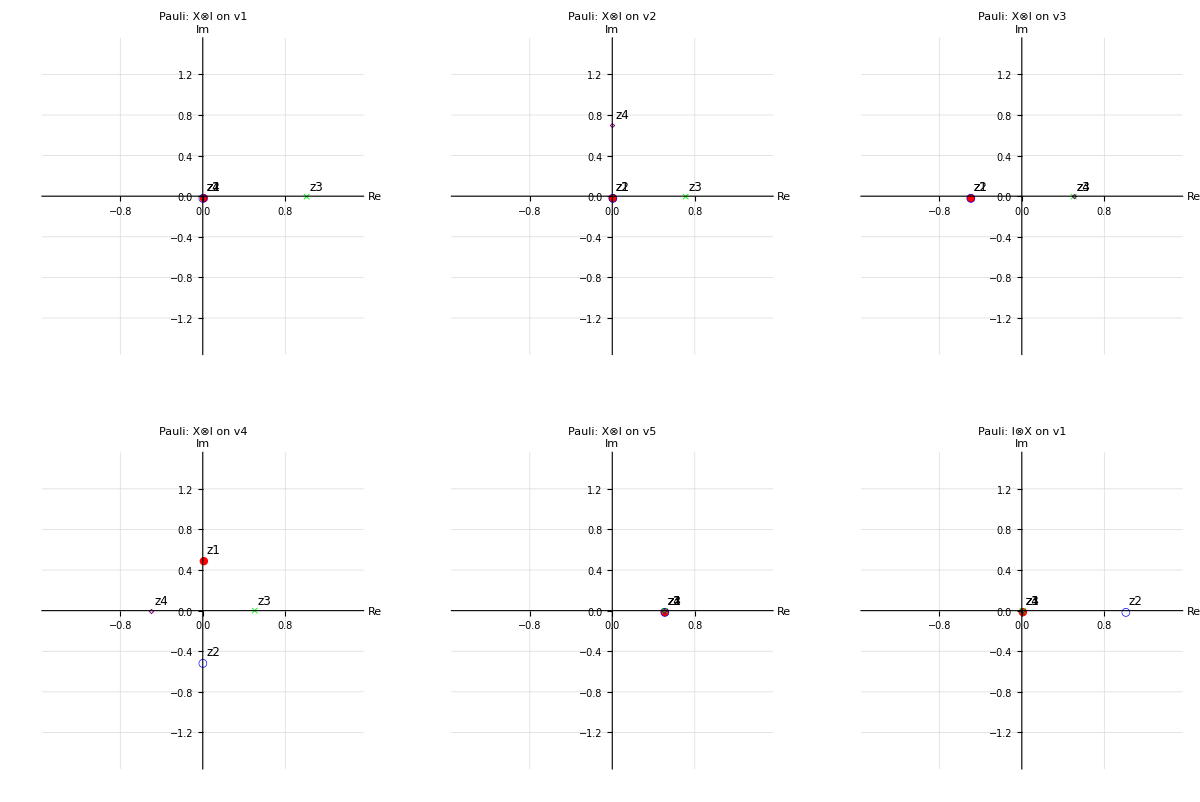

```mathematica
generatePlots[gates_,labels_,tag_]:=Flatten[Table[myPlot[gates[[g]].testVectors[[v]],tag<>": "<>labels[[g]]<>" on v"<>ToString[v]],{g,Length[gates]},{v,Length[testVectors]}]];

pauliPlots=generatePlots[pauliGates,pauliLabels,"Pauli"];
permPlots=generatePlots[permGates,permLabels,"Permutation"];
universalPlots=generatePlots[someUniversalGates,someUniversalLabels,"Universal"];
allPlots=Join[pauliPlots,permPlots,universalPlots];

GraphicsGrid[Partition[Take[allPlots,6],3]]
```

Generates labeled visualizations of how each gate transforms multiple test vectors, then organizes selected plots into a grid for comparative analysis

## Classifying Two-Qubit Gates Using Makhlin Invariant

The Need for Makhlin Invariants

In quantum computing, two-qubit gates are central to generating entanglement, which is the key resource for universality. However, a deep complication arises: many two-qubit gates that appear different are functionally identical when viewed through the lens of local equivalence—transformations of the form (U 1⊗U2)⋅V⋅(U3⊗U4) , where the U_i are single-qubit unitaries. These local gates do not change the entangling power or computational class of V, but they do change its matrix representation. Therefore, to classify truly distinct entangling operations, we need a tool that is invariant under local unitaries. This is where Makhlin invariants come into play: a trio of scalar quantities that remain unchanged under all local SU(2) ⊗ SU(2) conjugations and thus fully characterize the nonlocal content of a two-qubit gate.

The Mathemathical Framework

The Makhlin invariants (𝑔1,𝑔2,𝑔3)are computed by transforming the unitary gate U into a canonical form via the magic basis transformation K, yielding M=K^TKU.This basis diagonalizes certain Bell states and simplifies entanglement analysis. From M, we define m = M^TM and compute:
						`				g1 = (Tr m)^2/(det m)                      g2 = (Tr( m^2))/(det m)                  g3 = det m
These invariants are designed such that if two gates have identical Makhlin invariants, they are locally equivalent. Conversely, distinct invariants imply distinct nonlocal actions. Importantly, Makhlin invariants compress a 4×4 unitary down to just three numbers—serving as a hash function for quantum gate identity modulo local noise.

							d(U)=∥MakhlinInvariants(U)−MakhlinInvariants(CNOT)∥
							
and filter for gates with 𝑑(𝑈)<𝜖, where 𝜖 is a small tolerance to account for numerical imprecision. This ensures we retain only gates that are functionally equivalent to CNOT, a canonical universal entangler.

From a computer science perspective, this filtering process is essential for avoiding representation blowup and search inefficiency. Without Makhlin invariants, we’d be forced to test for local equivalence by brute-force optimization over local unitaries—a problem with a continuous search space and no closed-form solution. Makhlin invariants provide a constant-time fingerprint for local equivalence, enabling us to hash and group gates efficiently. In effect, they act as a collision-resistant function for quantum operations under local unitary equivalence, much like cryptographic hashes in classical computing. This transforms our infinite gate sampling process into a tractable and structured classification task.

```mathematica
representativeTriples=discreteWeylChamber;
XX=KroneckerProduct[{{0,1},{1,0}},{{0,1},{1,0}}];
YY=KroneckerProduct[{{0,-I},{I,0}},{{0,-I},{I,0}}];
ZZ=KroneckerProduct[{{1,0},{0,-1}},{{1,0},{0,-1}}];

buildRepresentativeGate[{c1_,c2_,c3_}]:=N[MatrixExp[I (c1 XX+c2 YY+c3 ZZ)],20];
representativeGates=buildRepresentativeGate/@representativeTriples;

K=(1/Sqrt[2])*{{1,0,0,I},{0,I,1,0},{0,I,-1,0},{1,0,0,-I}};

Kdag=ConjugateTranspose[K];
makhlinInvariants[U_]:=Module[{M,m,g1,g2,g3},M=Kdag.U.K;
m=Transpose[M].M;
g1=Tr[m]^2/Det[m];
g2=Tr[m.m]/Det[m];
g3=Det[m];
{g1,g2,g3}//Chop];

cnot={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
targetInvariants=makhlinInvariants[cnot];

invariantDistance[u_]:=Norm[makhlinInvariants[u]-targetInvariants];

universalGates=Select[representativeGates,invariantDistance[#]<1&];
```

```mathematica
Length[universalGates]
```

7

The results show that there are 7 gates in our set that are universal. Since our earlier focus was on identifying whether a gate is universal by comparing its Makhlin invariants to those of CNOT, we can now refine our perspective to consider efficiency — how close a universal gate is to a “minimal” entangling gate in the Cartan space. Traditionally, researchers group gates by conjugacy classes, treating any pair of gates equivalent under local operations as functionally identical. However, for practical quantum circuit design, conjugacy class membership is not enough, we need to evaluate how close a gate lies to CNOT in Cartan coordinates, because this affects how easily and efficiently we can approximate it using native gates. To measure this, we use a Cartan distance metric:

Measures how far a triple lies from the canonical CNOT location in the Weyl chamber

```mathematica
buildRepresentativeGate[{c1_,c2_,c3_}]:=MatrixExp[I (c1 XX+c2 YY+c3 ZZ)];

cartanDistance[{c1_,c2_,c3_}]:=Norm[{c1-Pi/4,c2,c3}];

shortestTriple=MinimalBy[universalTriples,cartanDistance][[1]];

mostEfficientGate=buildRepresentativeGate[shortestTriple];

MatrixForm[mostEfficientGate]
```

(1/(√2) | 0 | 0 | ⅈ/(√2)
0 | 1/(√2) | ⅈ/(√2) | 0
0 | ⅈ/(√2) | 1/(√2) | 0
ⅈ/(√2) | 0 | 0 | 1/(√2))

## Conclusion

The project shows that the  matrix returned, also known as the B gate is the most powerful and efficient universal two-qubit gate in the set studied. It is the closest gate to the canonical CNOT point in Cartan coordinates, which means it needs the least amount of entangling resources to achieve universality. This makes it highly practical for implementing any two-qubit operation with minimal overhead.The B gate’s matrix includes complex i terms in its off-diagonal elements, which give it strong entangling capabilities. These terms allow the gate to create maximal entanglement from certain input states. Maximal entanglement is essential for quantum algorithms and processes that rely on quantum correlations.

When decomposed into basic gates like CNOT and single-qubit rotations, the B gate typically requires fewer total gates and results in shallower circuits. This reduction in gate count and circuit depth improves performance on real quantum devices by lowering noise and error accumulation during execution.

This gate can be used as a native gate on quantum hardware to optimize circuit compilation. Implementing the B gate directly can lead to faster quantum computations since it closely approximates the ideal entangling gate needed for universal control over two qubits.

In conclusion, the B gate stands out as the most efficient universal two-qubit gate, combining strong entangling power with minimal resource requirements. It offers a clear advantage for building practical, high-fidelity quantum circuits and advancing the development of scalable quantum computing.

## Future Work

This project establishes a foundation for analyzing universal quantum gates and their efficiencies, but there is ample room for expansion. One important direction is to explore larger gate sets and multi-qubit systems, moving beyond two-qubit gates to tackle the scalability challenges essential for practical quantum computing. Additionally, incorporating noise models and error correction into gate synthesis and optimization would bring the work closer to real-world conditions by accounting for decoherence and operational imperfections. Another promising avenue is the development of automated synthesis algorithms that leverage machine learning or advanced heuristics to minimize gate depth, error rates, and resource overhead, improving gate compilation processes. Finally, investigating alternative universal gate sets beyond the Weyl chamber parametrization could identify more hardware-friendly or specialized gates, which, when combined with circuit-level optimizations, would enhance both theoretical understanding and experimental feasibility. Bridging the gap between mathematical universality, physical efficiency, and fault tolerance remains a rich field for continued research.

## Acknowledgements

I would like to sincerely thank my mentor, Adam Millar, for his invaluable guidance and support throughout this project. I am also grateful to the Wolfram directors and teaching assistants, whose insights and feedback played a crucial role in shaping my work.

## Works Cited

Barenco, Adriano, et al. “Elementary gates for quantum computation.” Physical Review A, vol. 52, no. 5, 1995, pp. 3457–3467. https://doi.org/10.1103/PhysRevA.52.3457

Bennett, Charles H., and David P. DiVincenzo. “Quantum information and computation.” Nature, vol. 404, 2000, pp. 247–255. https://doi.org/10.1038/35005001

Nielsen, Michael A., and Isaac L. Chuang. Quantum Computation and Quantum Information. Cambridge University Press, 2010.

Kitaev, Alexei Y. “Quantum computations: algorithms and error correction.” Russian Mathematical Surveys, vol. 52, no. 6, 1997, pp. 1191–1249. https://doi.org/10.1070/RM1997v052n06ABEH002155

Preskill, John. “Quantum computing in the NISQ era and beyond.” Quantum, vol. 2, 2018, Article 79. https://doi.org/10.22331/q-2018-08-06-79

Deutsch, David. “Quantum theory, the Church–Turing principle and the universal quantum computer.” Proceedings of the Royal Society A, vol. 400, no. 1818, 1985, pp. 97–117. https://doi.org/10.1098/rspa.1985.0070

Makhlin, Yuri. “Nonlocal properties of two-qubit gates and mixed states, and the optimization of quantum computations.” Quantum Information Processing, vol. 1, no. 4, 2002, pp. 243–252. https://doi.org/10.1023/A:1022144002391

Shor, Peter W. “Algorithms for quantum computation: Discrete logarithms and factoring.” Proceedings 35th Annual Symposium on Foundations of Computer Science, IEEE, 1994, pp. 124–134. https://doi.org/10.1109/SFCS.1994.365700

Bravyi, Sergey, and Alexei Kitaev. “Universal quantum computation with ideal Clifford gates and noisy ancillas.” Physical Review A, vol. 71, 2005, 022316. https://doi.org/10.1103/PhysRevA.71.022316

Morozov, A. “Hall Thruster Geometry.” Journal of Applied Physics, 2000. https://www.researchgate.net/publication/337085936_Thomson_scattering_investigations_of_a_low-power_Hall_thruster_in_standard_and_magnetically-shielded_configurations